```mathematica
Get[FileNameJoin[NotebookDirectory[],"init.wl"]];
Get[FileNameJoin[$toolsDirectory,"convertFrameData.wl"]];
Get[FileNameJoin[$toolsDirectory,"exactification.wl"]];
Get[FileNameJoin[$toolsDirectory,"inputOutput.wl"]];
Get[FileNameJoin[$toolsDirectory,"frameInvariants.wl"]];
Get[FileNameJoin[$toolsDirectory,"frameEquiv.wl"]];
Get[FileNameJoin[$toolsDirectory,"minimizationSetup.wl"]];
Get[FileNameJoin[$toolsDirectory,"validatePackings.wl"]];
```

```mathematica
(* MINIMIZATION EXAMPLES *)
{d,n}={3,13};
```

```mathematica
(* Example usage, one shot *)
min1=MinPhiQNp[rand[],20,WorkingPrecision->10];//Timing
```

{1.29688,Null}

```mathematica
min1[[1]]
min1[[2]]//Coherence
Welch[d,n]//N
```

0.006705847001

0.646065969

0.527046

```mathematica
(* Example usage, many shot *)
(* When searching for ETFs, it's probably best to do this with p=4; there is no need for multi-stage *)
comin=1;(* best coherence achieved so far; set to large dummy value to start *)
For[i=0,i<10,i++;
min1=MinPhiQNp[rand[],20,WorkingPrecision->10];
co1=Coherence[min1[[2]]];
{min,comin}=If[co1<comin,{min1,co1},{min,comin}]];//Timing//Quiet
```

{10.6563,Null}

```mathematica
min[[1]]
min[[2]]//Coherence
```

0.006705846642

0.646056589

```mathematica
(* Example usage, two-stage with many shot first stage *)
comin=1;(* best coherence achieved so far; set to large dummy value to start *)
For[i=0,i<10,i++;
min1=MinPhiQNp[rand[],20,WorkingPrecision->10];
co1=Coherence[min1[[2]]];
{min,comin}=If[co1<comin,{min1,co1},{min,comin}]];//Timing//Quiet
min=MinPhiQNp[min[[2]],40,WorkingPrecision->20];//Timing//Quiet
```

{12.5938,Null}

{11.,Null}

```mathematica
min[[1]]
min[[2]]//Coherence
```

5.2456686073256406219×10^-7

0.6328613818713926687

```mathematica
(* Finish with Principal Axes *)
minf=MinPhiPA[min[[2]],20,WorkingPrecision->2000];//Timing
```

{52.7969,Null}

```mathematica
(* Goal = 0.62214387 *)
frame=minf[[2]];
frame//Coherence
```

0.6270746835806691929

```mathematica
(* INPUT/OUTPUT EXAMPLES *)
```

```mathematica
(* Example import for (d,n)=(2,4) *)
etf = importPacking["etf_2x4_4a.gos"];
etf // mf
GMfromSO[etf] // mf
numberTP[etf]
exportPacking[etf,"output_example.gos"];
```

(1.+0. ⅈ | 0.57735+0. ⅈ | -0.288675-0.5 ⅈ | -0.288675+0.5 ⅈ
0.+0. ⅈ | 0.816497+0. ⅈ | 0.816497+0. ⅈ | 0.816497+0. ⅈ)

(1.+0. ⅈ | 0.57735+0. ⅈ | -0.288675-0.5 ⅈ | -0.288675+0.5 ⅈ
0.57735+0. ⅈ | 1.+0. ⅈ | 0.5-0.288675 ⅈ | 0.5+0.288675 ⅈ
-0.288675+0.5 ⅈ | 0.5+0.288675 ⅈ | 1.+0. ⅈ | 0.5-0.288675 ⅈ
-0.288675-0.5 ⅈ | 0.5-0.288675 ⅈ | 0.5+0.288675 ⅈ | 1.+0. ⅈ)

2

(1.+0. ⅈ | 0.57735+0. ⅈ | -0.288675-0.5 ⅈ | -0.288675+0.5 ⅈ
0.+0. ⅈ | 0.816497+0. ⅈ | 0.816497+0. ⅈ | 0.816497+0. ⅈ)

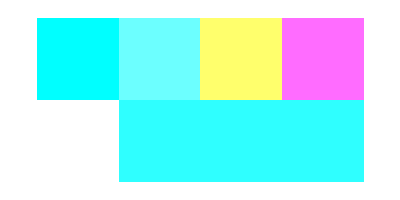

{1.,0.,0.57735,0.816497,-0.288675,0.816497,-0.288675,0.816497,0.,0.,0.,0.,-0.5,0.,0.5,0.}

(1.+0. ⅈ | 0.57735+0. ⅈ | -0.288675-0.5 ⅈ | -0.288675+0.5 ⅈ
0.+0. ⅈ | 0.816497+0. ⅈ | 0.816497+0. ⅈ | 0.816497+0. ⅈ)

(1.+0. ⅈ | 0.57735+0. ⅈ | -0.288675-0.5 ⅈ | -0.288675+0.5 ⅈ
0.57735+0. ⅈ | 1.+0. ⅈ | 0.5-0.288675 ⅈ | 0.5+0.288675 ⅈ
-0.288675+0.5 ⅈ | 0.5+0.288675 ⅈ | 1.+0. ⅈ | 0.5-0.288675 ⅈ
-0.288675-0.5 ⅈ | 0.5-0.288675 ⅈ | 0.5+0.288675 ⅈ | 1.+0. ⅈ)

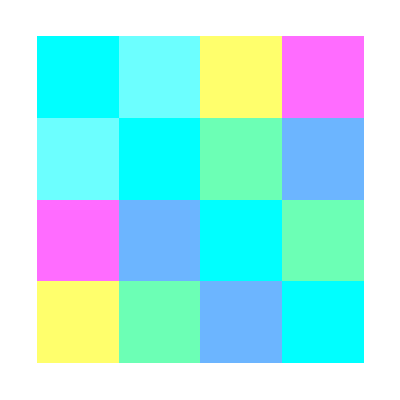

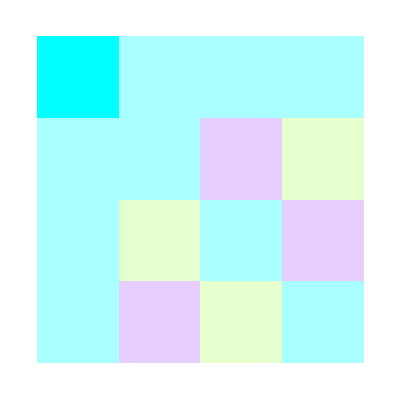
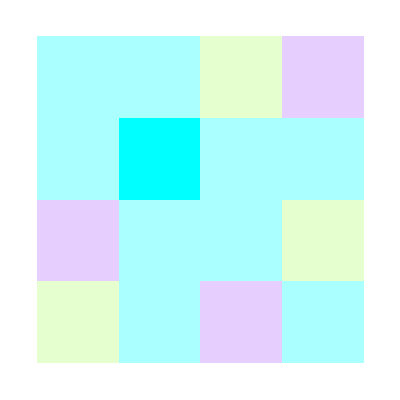
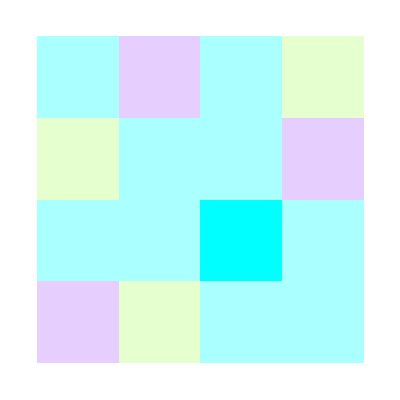
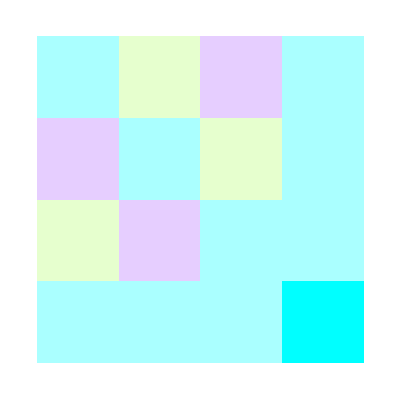

```mathematica
(* CONVERSION EXAMPLES *)
Phi=importPacking["etf_2x4_4a.gos"];Phi//N//mf
Phi//FrameVisualize
gos=GoSfromSO[Phi];gos
SOfromGoS[gos,{2,4}]//N//mf
G=GMfromSO[Phi];G//mf 
G//FrameVisualize
T=TPfromGM[G];
FrameVisualize/@T
```

```mathematica
(* EXACTIFICATION EXAMPLES *)
```

```mathematica
X/.NSolve[X^2-2==0,X,WorkingPrecision->10]
exactifyTuple[%]
```

{-1.414213562,1.414213562}

{-√2,√2}

```mathematica
X/.NSolve[X^2-2==0,X,WorkingPrecision->10]//Reverse
exactifyTuple[%]
```

{1.414213562,-1.414213562}

{√2,-√2}

```mathematica
arraytoLUT[{{1,1},{1,2}}]
arraytoLUT[{{1,1+10^(-5)},{1+10^(-10),2}}]
```

{{1,2},{{0,0},{0,1}}}

{{1,100001/100000,10000000001/10000000000,2},{{0,1},{2,3}}}

```mathematica
X/.NSolve[X^4-(1+Sqrt[2])==0,X,WorkingPrecision->10]//Reverse
exactifyTuple[%]//FullSimplify
N[%,10]
```

{1.246504703,1.246504703 ⅈ,-1.246504703 ⅈ,-1.246504703}

{(1+√2)^(1/4),ⅈ (1+√2)^(1/4),-ⅈ (1+√2)^(1/4),-(1+√2)^(1/4)}

{1.246504703,1.246504703 ⅈ,-1.246504703 ⅈ,-1.246504703}

```mathematica
(* EXACTIFICATION OF ETF EXAMPLE *)
```

```mathematica
Phiapprox = importPacking["etf_2x4_4a.gos"];
Tapprox=TPfromSO[Phiapprox];
Texact=exactifyTP[Tapprox];
SOexact=SOfromTP[Texact]//FullSimplify;
SOexact//mf
exportPacking[Texact,"etf_2x4_4a.tp"];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1/3+(-1/(2 √3)+(√3)/2)/(√3).

General::stop: Further output of N::meprec will be suppressed during this calculation.

((ⅈ+√3)/(√6) | ⅈ/(√2)+1/(√6) | 0 | √(2/3)
1/(√3) | -ⅈ/(√3) | 1 | ⅈ/(√3))

```mathematica
(* FRAME INVARIANTS EXAMPLE *)
```

```mathematica
numberTP[Phiapprox]
moment[Phiapprox,2]
momentnd[Phiapprox,2]
moment[SOexact,2]//FullSimplify
momentnd[SOexact,2]//FullSimplify
moment[Phiapprox,3]
momentnd[Phiapprox,3]
moment[SOexact,3]//FullSimplify
momentnd[SOexact,3]//FullSimplify
```

4

7.11111+0. ⅈ

-0.888889+0. ⅈ

64/9

-8/9

5.33333+0. ⅈ

8.29768×10^-18+0. ⅈ

16/3

0

```mathematica
(* FRAME EQUIVALENCE EXAMPLES *)
(* All tests should evaluate to True *)
Phi = importPacking["etf_2x4_4a.gos"];
dirtyFrameEquiv[Phi,Phi]
dirtyFrameEquiv[Phi,Phi+RandomReal[1,{2,4}]]//Not
dirtyFrameEquiv[Phi,Phi+10^(-10)RandomReal[1,{2,4}]]
dirtyFrameEquiv[Phi,Phi.PermutationMatrix[RandomPermutation[4],4].DiagonalMatrix[Exp[2π I RandomReal[1,4]]]]
randomInvariantFrameEquiv[Phi,Phi]
randomInvariantFrameEquiv[Phi,Phi+RandomReal[1,{2,4}]]//Not
randomInvariantFrameEquiv[Phi,Phi+10^(-10)RandomReal[1,{2,4}]]
randomInvariantFrameEquiv[Phi,Phi.PermutationMatrix[RandomPermutation[4],4].DiagonalMatrix[Exp[2π I RandomReal[1,4]]]]
fullFrameEquiv[Phi,Phi]
fullFrameEquiv[Phi,Phi+RandomReal[1,{2,4}]]//Not
fullFrameEquiv[Phi,Phi+10^(-10)RandomReal[1,{2,4}]]
fullFrameEquiv[Phi,Phi.PermutationMatrix[RandomPermutation[4],4].DiagonalMatrix[Exp[2π I RandomReal[1,4]]]]
```

True

True

True

«9 more identical outputs»

```mathematica
dirtyFrameEquiv[Phi,Phi*]
randomInvariantFrameEquiv[Phi,Phi*]
fullFrameEquiv[Phi,Phi*]
```

True

True

True